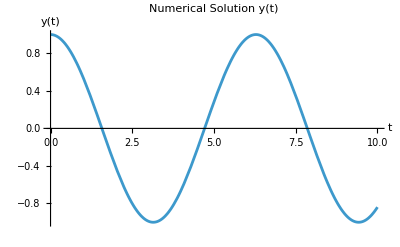

```mathematica
sol=NDSolve[{y''[t]+y[t]==0,y[0]==1,y'[0]==0},y,{t,0,10}];
Plot[y[t]/. sol,{t,0,10},PlotLabel->"Numerical Solution y(t)",AxesLabel->{"t","y(t)"}]
```

```mathematica
(*Define symbols*)A={{a11,a12},{a21,a22}};
b={b1,b2};
f[0]={f10,f20};

(*Differential equation system*)
eq=f'[x]==A.f[x]+b;

(*Solve analytically*)
sol=DSolve[{eq,f[0]=={f10,f20}},f[x],x]
```

DSolve::deqn: Equation or list of equations expected instead of True in the first argument {f'[x]=={b1+{{a11,a12},{a21,a22}}.f[x],b2+{{a11,a12},{a21,a22}}.f[x]},True}.

DSolve[{f'[x]=={b1+{{a11,a12},{a21,a22}}.f[x],b2+{{a11,a12},{a21,a22}}.f[x]},True},f[x],x]

```mathematica
Plot[y''[t]/. sol,{t,0,10},PlotLabel->"Numerical Solution y(t)",AxesLabel->{"t","y'(t)"}]
```

ReplaceAll::reps: {DSolve[{f'[x]=={b1+{«2»}.f[«1»],b2+{«2»}.f[«1»]},True},f[x],x]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

```mathematica
Manipulate[Module[{sol},sol=NDSolve[{y''[t]+ω^2 y[t]==0,y[0]==1,y'[0]==0},y,{t,0,10}];
Plot[Evaluate[y[t]/. sol],{t,0,10},PlotRange->All,PlotLabel->StringForm["Solution for ω = ``",ω],AxesLabel->{"t","y(t)"}]],{{ω,1,"Angular frequency (ω)"},0.1,5,0.1}]
```

```mathematica
Manipulate[Module[{sol,yFunc,yPrimeFunc,ke,pe,eTotal},(*Solve the ODE numerically*)sol=NDSolve[{y''[t]+ω^2 y[t]==0,y[0]==1,y'[0]==1},y,{t,0,10}];
(*Define functions*)yFunc[t_]=y[t]/. sol[[1]];
yPrimeFunc[t_]=y'[t]/. sol[[1]];
(*Energies*)ke[t_]=0.5 (yPrimeFunc[t])^2;
pe[t_]=0.5 ω^2 (yFunc[t])^2;
eTotal[t_]=ke[t]+pe[t];
(*Plot energies*)Plot[{ke[t],pe[t],eTotal[t]},{t,0,10},PlotRange->{0,1},PlotLegends->{"Kinetic Energy","Potential Energy","Total Energy"},PlotLabel->StringForm["Energy vs Time (ω = ``)",ω],AxesLabel->{"t","Energy"}]],{{ω,1,"Angular frequency (ω)"},0.1,5,0.1}]
```